Stochastic Solution Method of the Master Equation and the Model Boltzmann Equation

Kenichi Nanbu, Journal of the Physical Society of Japan, Vol.52, No 8, August, 1983, pp. 2654-2658 
Notebook: Óscar Amaro, October 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

## §2. Master Equation: example A

```mathematica
Clear[Wt,x,y]
(* Wt kernel is already normalized *)
Wt=π^(-1/2)Exp[-(x-y)^2];
Integrate[Wt,{y,-∞,∞}]
```

1

```mathematica
(* n-th moment for the Kramers-Moyal expansion *)
Clear[tmax,Δt,Nsmpl,pdf,cdf,x,y,Wt]
x=0;
pdf=1/√π  Exp[-(x-y)^2];
(*Integrate[(x-y)^2 pdf,{y,-∞,+∞}]*)
(*Refine[Integrate[Abs[(x-y)]^n pdf,{y,-∞,+∞}]//Normal,{n∈Integers,x∈Reals}]*)
2Integrate[y^n pdf,{y,0,+∞}]//Normal
```

Gamma[(1+n)/2]/(√π)

Simulation

(x̃)_(i,k) is sampled according to (W̃)_k(x|x_(i,k))
probability of transitioning to new "bin": P[x_(i,k+1)=(x̃)_(i,k)]=p_(i,k)
probability of nothing happening:P[x_(i,k+1)=x_(i,k)]=1-p_(i,k)
In this example, since the kernel is time-invariant and only depends on Δ=|x-y|, we can easily vectorize / parallelize the “Monte-Carlo” simulation. Also, the kernel is Gaussian, which allows efficient sampling (without resorting to Rejection or Inverse Transform methods).

```mathematica
Clear[tmax,Δt,Nsmpl,pdf,cdf,x,y,Wt,u,xlst,ulst,Δ,xmax,t00,t01,t02,t03,t05,t10,mul,mullst,Δlst]
tmax=10;
Δt=0.02;
nbins=20;
Nsmpl=3 10^4;
xmax=2;

xlst=RandomVariate[NormalDistribution[],{Nsmpl}]/2;
(*Histogram[xlst]*)
xbins=Table[x//N,{x,0,xmax,xmax/(nbins-1)}];
t00=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];

(* for time *)
For[t=0,t<=tmax, t=t+Δt,

(* transition? *)
ulst=RandomReal[{0,1},Nsmpl];
(* displacement *)
Δlst=RandomVariate[NormalDistribution[]]/√2;
(* [ulst[[i]]<Δt ? *)
mullst=Boole[Negative[ulst-Δt]];

(* new coordinate *)
xlst = xlst+Δlst mullst;

(* save histograms *)
If[Abs[t-1]<Δt/4,
t01=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-2]<Δt/4,
t02=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-3]<Δt/4,
t03=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-5]<Δt/4,
t05=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-10]<Δt/4,
t10=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
]
```

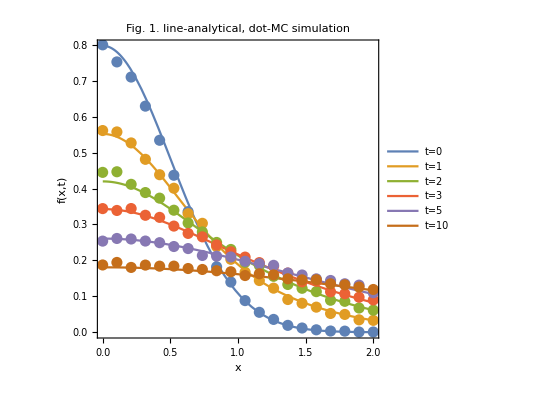

```mathematica
(* plot *)
Clear[t,x,f,a,n]
a=2;
(* normalize *)
mul=0.8/t00[[1]];

(* equation 14: analytical solution *)
f[t_,x_]:=Exp[-t] Sum[√((a/(n a +1))/π) t^n/(n!) Exp[-a/(n a +1)x^2],{n,0,20}]//Quiet

Show[{Plot[{f[0.001,x],f[1,x],f[2,x],f[3,x],f[5,x],f[10,x]},{x,0.001,2},AspectRatio->1,Frame->True,FrameLabel->{"x","f(x,t)"},PlotLabel->"Fig. 1. line-analytical, dot-MC simulation",PlotLegends->{"t=0","t=1","t=2","t=3","t=5","t=10"}],
ListPlot[{Transpose[{xbins,t00 mul}],Transpose[{xbins,t01 mul}],Transpose[{xbins,t02 mul}],Transpose[{xbins,t03 mul}],Transpose[{xbins,t05 mul}],Transpose[{xbins,t10 mul}]},Joined->False,PlotStyle->PointSize[0.02]]}]
```

## §2. Master Equation: example B

```mathematica
Clear[tmax,Δt,Nsmpl,pdf,cdf,x,y,Wt,u,xlst,ulst,Δ,xmax,t00,t01,t02,t05,t30,mul,mullst,Δlst]
tmax=3;
Δt=0.02;
nbins=20;
Nsmpl=3 10^4;
xmax=2;

xlst=-Log[RandomReal[{0,1},Nsmpl]];
(*Histogram[xlst]*)
xbins=Table[x//N,{x,0,xmax,xmax/(nbins-1)}];
t00=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];

(* for time *)
For[t=0,t<=tmax, t=t+Δt,

(* transition? *)
ulst=RandomReal[{0,1},Nsmpl];
(* displacement *)
Δlst=-Log[RandomReal[{0,1},Nsmpl]];
(* [ulst[[i]]<Δt ? *)
mullst=Boole[Negative[ulst-Exp[xlst]Δt]];

(* new coordinate: either stay (with probability (1-mullst) or move to x (with probability mullst, regardless of current xlst) *)
xlst = xlst(1-mullst)+Δlst mullst;

(* save histograms *)
If[Abs[t-0.1]<Δt/4,
t01=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-0.2]<Δt/4,
t02=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-0.5]<Δt/4,
t05=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
If[Abs[t-3]<Δt/4,
t30=BinCounts[xlst//Abs,{0,xmax,xmax/(nbins)}];
];
]
```

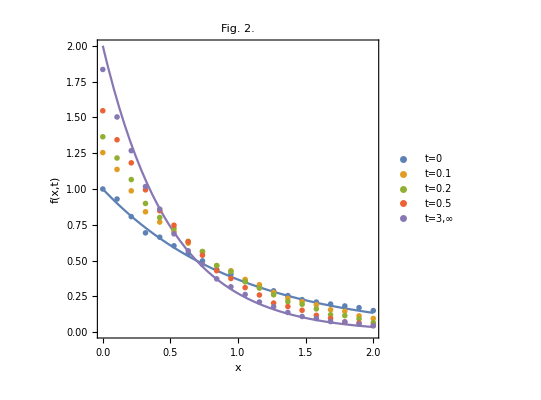

```mathematica
Clear[t,x,f,α,β]
α=β=1;
(* normalize *)
mul=1/t00[[1]];
Show[{Plot[{α Exp[-α x],-1,-1,-1,2β Exp[-2β x]},{x,0,2},AspectRatio->1,Frame->True,FrameLabel->{"x","f(x,t)"},PlotLabel->"Fig. 2.",PlotRange->{0,2}],
ListPlot[{Transpose[{xbins,t00 mul}],Transpose[{xbins,t01 mul}],Transpose[{xbins,t02 mul}],Transpose[{xbins,t05 mul}],Transpose[{xbins,t30 mul}]},Joined->False,PlotStyle->PointSize[0.02],PlotLegends->{"t=0","t=0.1","t=0.2","t=0.5","t=3,∞"},PlotMarkers->"OpenMarkers"]}]
```

## §3. Boltzmann Equation

```mathematica
Clear[t,x,y,xp,yp,f,c,dfdt,ν,θ]

(* equilibrium solution *)
f[x_]:=(c/π)^(1/2) Exp[-c x^2]

(* eq 17 *)
dfdt=ν/(2π)Integrate[Integrate[(f[x Cos[θ]+y Sin[θ]]f[-x Sin[θ]+y Cos[θ]]-f[x]f[y]),{θ,0,2π}],{y,-∞,+∞}]
(* so this is an equilibrium solution *)

(* equilibrium solution is normalized *)
Integrate[(c/π)^(1/2) Exp[-c x^2],{x,-∞,∞}]

(* E(t=0) *)
Et0=Integrate[x^2(2 x^2 Exp[-x^2])/π^(1/2),{x,-∞,∞}]

(* E(t->∞) *)
Et∞=Integrate[x^2(c/π)^(1/2) Exp[-c x^2],{x,-∞,∞}]

(* prove that c=1/3 *)
Solve[Et0==Et∞,c]
```

0

ConditionalExpression[1, Re[c]>0]

3/2

ConditionalExpression[1/(2 c), Re[c]>0]

{{c→1/3}}

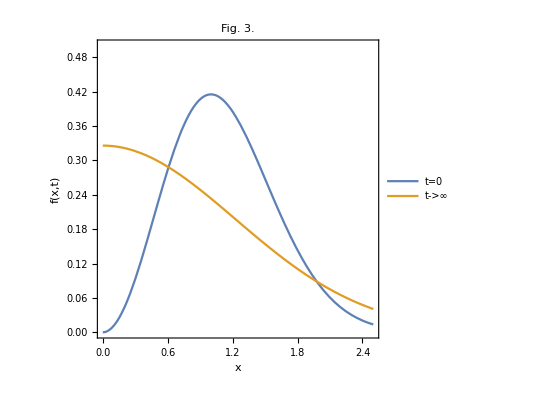

```mathematica
Clear[t,x,f,c]
c=1/3;
Plot[{(2 x^2 Exp[-x^2])/π^(1/2),(c/π)^(1/2)Exp[-c x^2]},{x,0,2.5},AspectRatio->1,Frame->True,FrameLabel->{"x","f(x,t)"},PlotLabel->"Fig. 3.",PlotLegends->{"t=0","t->∞"},PlotRange->{0,0.5}]
```